```mathematica
Needs["ExperimentEvaluation`"]
```

```mathematica
labels=Flatten[Outer[StringJoin,{"GPAT_","GP_"},{"H","H2"}]]
```

{GPAT_H,GPAT_H2,GP_H,GP_H2}

```mathematica
data=readAllFiles[{"20110803/GP4D_1000","GPAT4D_SSM_500"},labels,ReplaceParamValues->{"FC55"->"ZFC55"}];
```

```mathematica
data=readAllFiles[{"GPAT3D_H_H2_200","GP3D_H_200","GP3D_H2_200"},labels];
```

```mathematica
data=readAllFiles[{"GP4D_E_200","GPAT4D_E_200","GPAT4D_E_200_NOREPEAT","GPAT4D_E_200_TC"},{"GP_E","GPAT_E","GPAT_E_NR","GPAT_E_TC"}];
```

```mathematica
changingParameters[data]
```

{GP.MAX_EVALUATIONS,GP.MUTATION_CAUCHY_PROBABILITY,GP.TYPE,SOLVER}

```mathematica
sortedData=sortDataByParams[data,{"SYMBOLIC_REGRESSION_4D.F","SOLVER","GPAT.SPECIES_SIZE_MEAN"},ReplaceParamValues->{"ZFC55"->"FC55"}];
```

```mathematica
saveData[sortedData,"GPAT4D_SSM_500"]
```

```mathematica
printAsTable[sortedData,{"SOLVER","SYMBOLIC_REGRESSION_4D.F","GPAT.SPECIES_SIZE_MEAN"}]
```

ID | PARAM FILE | SOLVER | SYMBOLIC_REGRESSION_4D.F | GPAT.SPECIES_SIZE_MEAN
GP_E | GP4D_E_200/parameters_001.txt | GP | E | NONE
GPAT_E | GPAT4D_E_200/parameters_001.txt | GPAT | E | 20.
GPAT_E_NR | GPAT4D_E_200_NOREPEAT/parameters_001.txt | GPAT | E | 20.
GPAT_E_TC | GPAT4D_E_200_TC/parameters_001.txt | GPAT | E | 20.

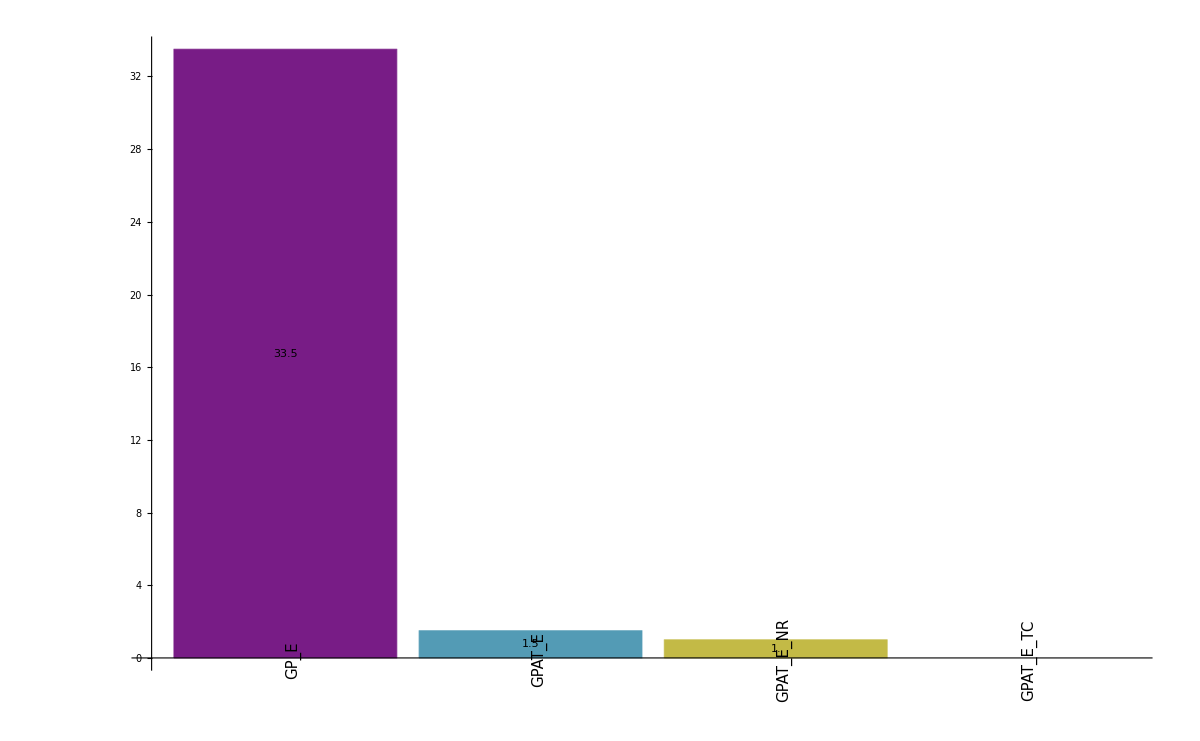

```mathematica
plotBooleanAsBarChart[sortedData,"SUCCESS"]
```

```mathematica
plotAsBoxWhiskerChart[sortedData,"BSF"];
```

```mathematica
testMannWhitney[data,"GPAT_H","GPAT_H2","BSF"]
```

median 1: 0.952853

median 2: 0.949325

mean 1: 0.754262

mean 2: 0.528663

variance 1: 0.135817

variance 2: 0.222969

higher/lower variance ratio: 1.64169

U stat: 22636

P-value: 0.0226329

The null hypothesis that the median difference is 0 is rejected at the 5. percent level based on the Mann-Whitney test.

```mathematica
testKruskalWallis[data,{"GPAT_H","GPAT_H2"},"BSF"]
```

| GPAT_H | GPAT_H2
Mean | 0.754262 | 0.528663
Variance | 0.952853 | 0.949325
Variance | 0.135817 | 0.222969

LocationEquivalenceTest::ntsymmd: The p-value in 1.14305×10^-13, resulting from a test for symmetry, is below 0.05. The tests in {"KruskalWallis"} require that the data is symmetric about a common median.

| Statistic | P-Value
Kruskal-Wallis | 5.19838 | 0.0224202

```mathematica
testFisherExact[sortedData,"GPAT_H","GPAT_H2","SUCCESS",TwoSided->True]
```

| GPAT_H | GPAT_H2
true | 133. | 100.
false | 67. | 100.

0.00114716

```mathematica
sortConfigurationResults[sortedData,"GPAT_E_TC","BSF",10]
```

189 | 0.888889
48 | 0.888889
109 | 0.888889
151 | 0.888889
174 | 0.888889
44 | 0.888889
55 | 0.888889
29 | 0.888889
124 | 0.888889
144 | 0.888889

```mathematica
Expand[1.5*x1*x2+2.3*x1+x2*x3*x4-1.1*x3]
```

2.3 x1+1.5 x1 x2-1.1 x3+x2 x3 x4

```mathematica
(res=sortConfigurationResults[sortedData,"GP_E","BSF",10,Output->"Expressions"]/.{x0->Subscript[x, 1],x1->Subscript[x, 2],x2->Subscript[x, 3],x3->Subscript[x, 4]})
```

Gen | Expression | Expanded | f
last | {x_1+x_1 (1.29934+1.49921 x_2)+x_3 (-1.+x_2 x_4)} | {2.29934 x_1+1.49921 x_1 x_2-1. x_3+x_2 x_3 x_4} | 0.995025
last | {1.96928 x_1+x_1 (0.326547+1.49676 x_2)+x_3 (-1.+x_2 x_4)} | {2.29583 x_1+1.49676 x_1 x_2-1. x_3+x_2 x_3 x_4} | 0.995014
last | {2 x_1+1.49102 x_1 (0.202711+x_2)+x_3 (-1.+x_2 x_4)} | {2.30225 x_1+1.49102 x_1 x_2-1. x_3+x_2 x_3 x_4} | 0.995002
last | {2.30277 x_1+2.04003 ArcTan[0.864505 x_2] x_1+x_3 (-1.+x_2 x_4)} | {2.30277 x_1+2.04003 ArcTan[0.864505 x_2] x_1-1. x_3+x_2 x_3 x_4} | 0.993268
last | {Sin[x_1] (ArcTan[Sin[x_2]]+x_2)-1. (-2.30021 x_1+x_3)+x_2 x_3 x_4} | {ArcTan[Sin[x_2]] Sin[x_1]+2.30021 x_1+Sin[x_1] x_2-1. x_3+x_2 x_3 x_4} | 0.992255
last | {(1.75347+ArcTan[0.793594+x_2]) x_1-1.10017 x_3+Sin[x_2] (x_1+x_3 x_4)} | {1.75347 x_1+ArcTan[0.793594+x_2] x_1+Sin[x_2] x_1-1.10017 x_3+Sin[x_2] x_3 x_4} | 0.992159
last | {1.49829 Sin[x_1]+x_1+2 ArcTan[x_1] x_2-1.09991 x_3+x_2 x_3 x_4} | {1.49829 Sin[x_1]+x_1+2 ArcTan[x_1] x_2-1.09991 x_3+x_2 x_3 x_4} | 0.990323
last | {(2.29917+ArcTan[x_2]+Sin[x_2]) x_1+x_3 (-1.09996+x_2 x_4)} | {2.29917 x_1+ArcTan[x_2] x_1+Sin[x_2] x_1-1.09996 x_3+x_2 x_3 x_4} | 0.989438
last | {x_1+ArcTan[x_1] (1.58978+2 x_2)+x_3 (-1.05568+x_2 x_4)} | {1.58978 ArcTan[x_1]+x_1+2 ArcTan[x_1] x_2-1.05568 x_3+x_2 x_3 x_4} | 0.987789
last | {x_1+x_1 (0.811761+ⅇ^(-(-0.905095+x_2)^2)+x_2)+x_3 (-0.95592+x_2 x_4)} | {1.81176 x_1+ⅇ^(-(-0.905095+x_2)^2) x_1+x_1 x_2-0.95592 x_3+x_2 x_3 x_4} | 0.987207

```mathematica
(res=sortConfigurationResults[sortedData,"GPAT_E","BSF",10,Output->"Expressions"]/.{x0->Subscript[x, 1],x1->Subscript[x, 2],x2->Subscript[x, 3],x3->Subscript[x, 4]})
```

Gen | Expression | Expanded | f
last | {2.31038 x_1-1.10689 x_3-0.269243 x_2 (-4.66857 x_1-3.34814 x_2^2 x_3 x_4)} | {2.31038 x_1+1.25698 x_1 x_2-1.10689 x_3+0.901463 x_2^3 x_3 x_4} | 0.970107
last | {-1.06536 x_3+1.28824 (1.60363 x_1+1.37067 x_1 x_2+0.939168 x_2 x_3 x_4)} | {2.06586 x_1+1.76574 x_1 x_2-1.06536 x_3+1.20987 x_2 x_3 x_4} | 0.95132
last | {2.32435 x_1+1.48058 x_1 x_2-1.06271 x_3+1.16641 x_1^2 x_2 x_3 x_4} | {2.32435 x_1+1.48058 x_1 x_2-1.06271 x_3+1.16641 x_1^2 x_2 x_3 x_4} | 0.950063
last | {-1.10012 x_3+0.56686 (4.05415 x_1+2.63554 x_1 x_2+2.18541 x_1^2 x_2 x_3^5 x_4^3)} | {2.29813 x_1+1.49398 x_1 x_2-1.10012 x_3+1.23882 x_1^2 x_2 x_3^5 x_4^3} | 0.933609
last | {2.30023 x_1+0.978406 ArcTan[4 x_1+x_3^3 x_4] x_2-1.09987 x_3} | {2.30023 x_1+0.978406 ArcTan[4 x_1+x_3^3 x_4] x_2-1.09987 x_3} | 0.900382
last | {2.28705 x_1-1.09339 x_3-0.942131 x_1 (-1.48579 x_2-0.109345 x_1 x_2 x_3 x_4)} | {2.28705 x_1+1.39981 x_1 x_2-1.09339 x_3+0.103017 x_1^2 x_2 x_3 x_4} | 0.896618
last | {2.29978 x_1+1.04596 ArcTan[ⅇ^(-(1+x_4)^2)+3 x_1+x_4+x_3 x_4^5] x_2-1.09985 x_3} | {2.29978 x_1+1.04596 ArcTan[ⅇ^(-(1+x_4)^2)+3 x_1+x_4+x_3 x_4^5] x_2-1.09985 x_3} | 0.890725
last | {2.30005 x_1+1.49995 x_1 x_2-1.10006 x_3} | {2.30005 x_1+1.49995 x_1 x_2-1.10006 x_3} | 0.888889
last | {2.30001 x_1+1.49994 x_1 x_2-1.09992 x_3} | {2.30001 x_1+1.49994 x_1 x_2-1.09992 x_3} | 0.888889
last | {2.29999 x_1+1.50008 x_1 x_2-1.10007 x_3} | {2.29999 x_1+1.50008 x_1 x_2-1.10007 x_3} | 0.888889

```mathematica
(res=sortConfigurationResults[sortedData,"GPAT_E_NR","BSF",10,Output->"Expressions"]/.{x0->Subscript[x, 1],x1->Subscript[x, 2],x2->Subscript[x, 3],x3->Subscript[x, 4]})
```

Gen | Expression | Expanded | f
last | {2.31623 x_1-0.795326 x_3-0.738066 x_2 (-2.03725 x_1-1.4899 x_3 x_4)} | {2.31623 x_1+1.50363 x_1 x_2-0.795326 x_3+1.09964 x_2 x_3 x_4} | 0.95439
last | {1.5364 ArcTan[0.328835 x_1+x_1 x_2+0.0196114 x_3+0.87757 x_2 x_3 x_4]+2.02636 x_1-1.18157 x_3} | {1.5364 ArcTan[0.328835 x_1+x_1 x_2+0.0196114 x_3+0.87757 x_2 x_3 x_4]+2.02636 x_1-1.18157 x_3} | 0.9523
last | {-1.77562 ArcTan[x_2+x_3+x_4]+2.2962 x_1+1.07271 x_2+1.49574 x_1 x_2+1.07166 x_4} | {-1.77562 ArcTan[x_2+x_3+x_4]+2.2962 x_1+1.07271 x_2+1.49574 x_1 x_2+1.07166 x_4} | 0.939324
last | {2.15801 ArcTan[x_1+x_1 x_2+0.562783 x_2 x_3 x_4]+0.791749 x_1-1.10121 x_3} | {2.15801 ArcTan[x_1+x_1 x_2+0.562783 x_2 x_3 x_4]+0.791749 x_1-1.10121 x_3} | 0.93306
last | {1.31123 (1.47009 ArcTan[x_1+x_1 x_2+x_2 x_3 x_4]+0.739914 x_1-0.83783 x_3)} | {1.92762 ArcTan[x_1+x_1 x_2+x_2 x_3 x_4]+0.970197 x_1-1.09859 x_3} | 0.901868
last | {0.448848 (4.48252 ArcTan[x_1+x_1 x_2+x_2 x_3 x_4]+2.04508 x_1-2.49772 x_3)} | {2.01197 ArcTan[x_1+x_1 x_2+x_2 x_3 x_4]+0.917931 x_1-1.1211 x_3} | 0.900676
last | {2.30731 x_1+1.51345 x_1 x_2-1.09274 x_3+0.475634 ArcTan[1+x_1+x_2+x_3+x_4] x_1 x_2 x_3 x_4} | {2.30731 x_1+1.51345 x_1 x_2-1.09274 x_3+0.475634 ArcTan[1+x_1+x_2+x_3+x_4] x_1 x_2 x_3 x_4} | 0.899273
last | {2.3223 x_1+1.12301 ArcTan[5.33451-3.78576 Sin[x_1+x_2+x_3+x_4]+1.09686 x_1+0.288484 x_2+0.567205 x_3+0.253478 x_4] x_1 x_2-1.12824 x_3} | {2.3223 x_1+1.12301 ArcTan[5.33451-3.78576 Sin[x_1+x_2+x_3+x_4]+1.09686 x_1+0.288484 x_2+0.567205 x_3+0.253478 x_4] x_1 x_2-1.12824 x_3} | 0.895077
last | {2.28671 x_1+1.47967 x_1 x_2-1.09195 x_3-0.544571 Sin[1+x_1+x_2+x_3+x_4] x_1^2 x_2^2 x_3 x_4^2} | {2.28671 x_1+1.47967 x_1 x_2-1.09195 x_3-0.544571 Sin[1+x_1+x_2+x_3+x_4] x_1^2 x_2^2 x_3 x_4^2} | 0.89326
last | {2.31855 x_1+0.015061 x_2+1.65201 Sin[1+ⅇ^(-(1+x_1+x_2+x_3+x_4)^2)] x_1 x_2-1.11156 x_3} | {2.31855 x_1+0.015061 x_2+1.65201 Sin[1+ⅇ^(-(1+x_1+x_2+x_3+x_4)^2)] x_1 x_2-1.11156 x_3} | 0.890838

```mathematica
(res=sortConfigurationResults[sortedData,"GPAT_E_TC","BSF",10,Output->"Expressions"]/.{x0->Subscript[x, 1],x1->Subscript[x, 2],x2->Subscript[x, 3],x3->Subscript[x, 4]})
```

Gen | Expression | Expanded | f
last | {2.30005 x_1-0.899958 (-1.66674 x_1 x_2+1.22237 x_3)} | {2.30005 x_1+1.5 x_1 x_2-1.10008 x_3} | 0.888889
last | {2.29997 x_1-0.372075 (-4.03104 x_1 x_2+2.95641 x_3)} | {2.29997 x_1+1.49985 x_1 x_2-1.1 x_3} | 0.888889
last | {2.29998 x_1-0.334094 (-4.48919 x_1 x_2+3.29259 x_3)} | {2.29998 x_1+1.49981 x_1 x_2-1.10003 x_3} | 0.888889
last | {2.29988 x_1-0.350183 (-4.28333 x_1 x_2+3.14105 x_3)} | {2.29988 x_1+1.49995 x_1 x_2-1.09994 x_3} | 0.888889
last | {2.30005 x_1-2.66549 (-0.562716 x_1 x_2+0.412724 x_3)} | {2.30005 x_1+1.49992 x_1 x_2-1.10011 x_3} | 0.888889
last | {2.30005 x_1+0.23843 (6.29191 x_1 x_2-4.61344 x_3)} | {2.30005 x_1+1.50018 x_1 x_2-1.09998 x_3} | 0.888889
last | {1.00142 x_1 (2.2967+1.49775 x_2)-1.0999 x_3} | {2.29996 x_1+1.49987 x_1 x_2-1.0999 x_3} | 0.888889
last | {2.30008 x_1+0.284138 (5.27927 x_1 x_2-3.87085 x_3)} | {2.30008 x_1+1.50004 x_1 x_2-1.09985 x_3} | 0.888889
last | {2.29984 x_1-0.363577 (-4.12556 x_1 x_2+3.02534 x_3)} | {2.29984 x_1+1.49996 x_1 x_2-1.09995 x_3} | 0.888889
last | {2.30005 x_1+0.499116 (3.00497 x_1 x_2-2.20412 x_3)} | {2.30005 x_1+1.49983 x_1 x_2-1.10011 x_3} | 0.888889

```mathematica
Export["GP_H2.pdf",%]
```

GP_H2.pdf